# TensorNetworks: Complete Examples

This notebook demonstrates all functions in Wolfram`TensorNetworks` with detailed examples including formulas, explanations, and quantum applications.

## Setup

```mathematica
PacletDirectoryLoad["/Users/mohammadb/Documents/GitHub/TensorNetworks"]
Needs["Wolfram`TensorNetworks`"]
```

{/Users/mohammadb/Documents/GitHub/TensorNetworks}

## Core Tensor Network Construction

TensorNetwork creates a tensor network from tensors and their index structure
at a minimal level, one needs a list of tensor and some notation for indices that specify where einsum/contraction is being done (one can imagine it as Inactive[TensorContract][Inactive[TensorProduct][tensors],slots of contractions])

```mathematica
t1=RandomComplex[{-1-I,1+I},{3,2,3}];
t2=RandomComplex[{-1-I,1+I},{2,3}];
t3=RandomComplex[{-1-I,1+I},{4,3,2,3}];
tn=TensorNetwork[{t1,t2,t3},{{1,2,3},{2,1},{4,3,2,5}}]
```

TensorNetwork[…]

```mathematica
TensorNetworkQ[tn]
```

True

Expression of contraction for TN

```mathematica
TensorNetworkContraction[tn]
```

TensorContract[{{{-0.589697+0.845804 ⅈ,0.962237-0.482182 ⅈ,0.0240365+0.220518 ⅈ},{0.339493+0.812992 ⅈ,-0.845373-0.0419222 ⅈ,-0.58568+0.00438448 ⅈ}},{{0.984323-0.711758 ⅈ,0.697781+0.824607 ⅈ,0.8991-0.400146 ⅈ},{0.0270889-0.0955154 ⅈ,-0.680447-0.253608 ⅈ,-0.597333-0.0739931 ⅈ}},{{-0.125364-0.453243 ⅈ,0.809463+0.0759319 ⅈ,0.516797-0.555371 ⅈ},{0.27655-0.228207 ⅈ,0.919429-0.179964 ⅈ,-0.491773+0.438205 ⅈ}}}⊗{{0.133603+0.545992 ⅈ,-0.953218+0.0413738 ⅈ,0.476657-0.250099 ⅈ},{-0.340191+0.447421 ⅈ,-0.396414+0.746072 ⅈ,-0.672503-0.383503 ⅈ}}⊗{{{{-0.866829+0.497785 ⅈ,-0.46107+0.806235 ⅈ,-0.863784-0.130052 ⅈ},{-0.417405+0.521783 ⅈ,0.403464+0.588184 ⅈ,0.753219+0.218046 ⅈ}},{{0.118428-0.465317 ⅈ,0.156944+0.773182 ⅈ,0.514637+0.618521 ⅈ},{0.966794+0.985842 ⅈ,-0.342989-0.625636 ⅈ,-0.0644174-0.594048 ⅈ}},{{0.481145+0.460624 ⅈ,0.60972+0.0917187 ⅈ,0.108079-0.685812 ⅈ},{0.537706-0.901548 ⅈ,0.887176-0.919318 ⅈ,0.263663-0.14327 ⅈ}}},{{{-0.49482-0.629003 ⅈ,-0.841125+0.328203 ⅈ,-0.717842-0.0624937 ⅈ},{-0.914841-0.516481 ⅈ,0.668336-0.220274 ⅈ,-0.808867-0.689595 ⅈ}},{{0.84901+0.202948 ⅈ,0.727065-0.857389 ⅈ,-0.266356-0.256445 ⅈ},{0.4732+0.952502 ⅈ,0.451848+0.58878 ⅈ,-0.103317-0.685778 ⅈ}},{{0.176942-0.937027 ⅈ,0.705634+0.41346 ⅈ,-0.199879+0.984609 ⅈ},{-0.17214+0.700661 ⅈ,-0.141707+0.49874 ⅈ,-0.291363-0.507048 ⅈ}}},{{{0.221906+0.712793 ⅈ,-0.91661-0.195978 ⅈ,-0.871578+0.532449 ⅈ},{0.895863+0.0741928 ⅈ,-0.415986-0.923714 ⅈ,-0.382751+0.485478 ⅈ}},{{-0.151206+0.590872 ⅈ,-0.450749-0.0885985 ⅈ,0.99568-0.107788 ⅈ},{-0.0584604+0.461787 ⅈ,0.333855-0.0402627 ⅈ,-0.188838+0.394228 ⅈ}},{{0.522725-0.629086 ⅈ,-0.193472-0.482311 ⅈ,0.0949444-0.568351 ⅈ},{-0.144183+0.163465 ⅈ,0.572848-0.687466 ⅈ,-0.685949-0.991035 ⅈ}}},{{{0.801578-0.0716395 ⅈ,0.44086+0.572056 ⅈ,-0.375314+0.771861 ⅈ},{0.485327+0.698074 ⅈ,-0.110215-0.0127513 ⅈ,-0.962344-0.466921 ⅈ}},{{0.22417-0.63423 ⅈ,0.448504-0.185539 ⅈ,0.0156906-0.767621 ⅈ},{0.659153-0.913742 ⅈ,0.400671+0.736942 ⅈ,0.488019-0.268019 ⅈ}},{{-0.920593+0.205031 ⅈ,-0.378425-0.706002 ⅈ,0.76846+0.872675 ⅈ},{0.606768-0.468599 ⅈ,0.836391-0.37638 ⅈ,-0.251178-0.140838 ⅈ}}}}⊗2,2,21,2,3,{{1,5},{2,10},{3,7},{4,11},{8,12}}]

Making tensors as sparse array (maybe memory save?)

```mathematica
TensorNetworkContraction[SparseTensorNetwork@tn]
```

TensorContract[SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗2,2,21,2,3,{{1,5},{2,10},{3,7},{4,11},{8,12}}]

SparseTensorNetwork converts tensors in a TN to SparseArray form for memory efficiency. but not sure if it is a good name bc only replacing head might not help esp since tensors are generated by RandomComplex or RandomReal

Execute the contraction

```mathematica
TensorNetworkContract[tn]
```

{{1.7862-4.10832 ⅈ,-0.434098-3.21786 ⅈ,0.76427-0.153457 ⅈ},{3.09264+2.09766 ⅈ,0.715156-1.19352 ⅈ,0.30887-0.613654 ⅈ},{-0.909919-0.0858913 ⅈ,1.94464-0.20349 ⅈ,0.443614-1.67768 ⅈ},{-1.73594-2.18907 ⅈ,0.802355-1.79793 ⅈ,-0.640193-2.25715 ⅈ}}

```mathematica
data=TensorNetworkData[SparseTensorNetwork@tn]
```

<|Tensors→{SparseArray[…],SparseArray[…],SparseArray[…]},Dimensions→{{3,2,3},{2,3},{4,3,2,3}},Indices→{{1^1,1^2,1^3},{2^2,2^1},{3^4,3^3,3^2,3^5}},Vertices→{1,2,3},FreeIndices→{3^4,3^5},Bonds→{{1^1,2^1}→3,{1^2,2^2,3^2}→2,{1^3,3^3}→3},Contractions→{{{1^1,2^1},{1^2,2^2,3^2},{1^3,3^3}},{{1^2,2^2,3^2},{1^1,2^1}},{3^4,{1^3,3^3},{1^2,2^2,3^2},3^5}},ContractionIndices→{{1^1,1^2,1^3},{1^2,1^1},{3^4,1^3,1^2,3^5}}|>

list of tensors

```mathematica
TensorNetworkTensors[tn]==data["Tensors"]
```

True

local indices of tensors (the contraction info is encoded in the superscripts)

```mathematica
data["Indices"]
```

{{1^1,1^2,1^3},{2^2,2^1},{3^4,3^3,3^2,3^5}}

Global indices of tensors, this time with explicit info of contractions (repeated are contracted)

```mathematica
TensorNetworkIndices[tn]
%==data["ContractionIndices"]
```

{{1^1,1^2,1^3},{1^2,1^1},{3^4,1^3,1^2,3^5}}

True

Global indices and their dimensions:

```mathematica
TensorNetworkIndexDimensions[tn]
```

{1^1→3,1^2→2,1^3→3,2^2→2,2^1→3,3^4→4,3^3→3,3^2→2,3^5→3}

indices of each tensor, if paired/listed with another one it means it will be contracted. If no list, it means it will be a free index

```mathematica
TensorNetworkContractions[tn]
%==data["Contractions"]
```

{{{1^1,2^1},{1^2,2^2,3^2},{1^3,3^3}},{{1^2,2^2,3^2},{1^1,2^1}},{3^4,{1^3,3^3},{1^2,2^2,3^2},3^5}}

True

Indices that are not being contracted

```mathematica
TensorNetworkFreeIndices@tn
```

{3^4,3^5}

Hypergraph of TN:

```mathematica
tn["Hypergraph"]
```

-Graphics-

Hyperedges:

```mathematica
tn["Hyperedges"]
```

{{1,2,3},{2,1},{4,3,2,5}}

As one can see above, the second index is shared by three tensors, meaning it is not a pairwise/binary tensor

```mathematica
BinaryTensorNetworkQ[tn]
```

False

```mathematica
Names["*TensorNetwork*"]
```

{BinaryTensorNetwork,BinaryTensorNetworkQ,InitializeTensorNetwork,RandomTensorNetwork,SparseTensorNetwork,TensorNetwork,TensorNetworkAdd,TensorNetworkContract,TensorNetworkContraction,TensorNetworkContractions,TensorNetworkData,TensorNetworkFindContractionPath,TensorNetworkFreeIndices,TensorNetworkGraphData,TensorNetworkGraphQ,TensorNetworkIndexDimensions,TensorNetworkIndexGraph,TensorNetworkIndices,TensorNetworkQ,TensorNetworkRemoveCycles,TensorNetworkReplaceIndices,TensorNetworkSize,TensorNetworkTensors,TensorNetworkToNetGraph,ToTensorNetworkGraph,$TensorNetworkContractionMethods}

To transform a TN that is not pairwise/binary, one can add symbolic delta-product tensor at the right places

```mathematica
BinaryTensorNetwork[SparseTensorNetwork@tn]["Tensors"]
```

{SparseArray[…],SparseArray[…],SparseArray[…],2,2,21,2,3}

```mathematica
Row[{tn["Hypergraph"],"⟶",BinaryTensorNetwork[tn]["Hypergraph"]}]
```

-Graphics-⟶-Graphics-

Since graph is always binary, if one asks for Graph of a TN, one gets automatically a spider (symbolic delta-product tensor) added

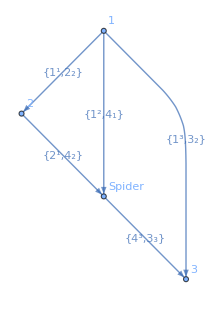

```mathematica
Graph[tn["Graph"],EdgeLabels->Automatic]
```

## Graph and Topology

### ToTensorNetworkGraph

Constructs a TensorNetwork from a graph with tensor data at vertices.

```mathematica
tng=ToTensorNetworkGraph[g=RandomGraph[{4,3}],Method->"RandomComplex"]
```

-Graphics-

```mathematica
TensorNetworkGraphQ[tng]
```

True

```mathematica
TensorNetworkGraphData[tng]
```

<|Tensors→{{-0.615629+0.967581 ⅈ,-0.416677+0.171493 ⅈ},{-0.118767+0.183218 ⅈ,-0.977728+0.331289 ⅈ},{{0.233978-0.623686 ⅈ,0.107698-0.28962 ⅈ},{0.459605-0.592967 ⅈ,0.351441+0.556123 ⅈ}},{{-0.641398-0.986184 ⅈ,-0.0643384-0.655265 ⅈ},{0.590714+0.821842 ⅈ,0.789655+0.799814 ⅈ}}},Dimensions→{{2},{2},{2,2},{2,2}},Indices→{{3^1},{1^2},{2^2,2_2},{4_1,4_2}},Vertices→{3,1,2,4},FreeIndices→{},Bonds→{{3^1,4_1}→2,{1^2,2_2}→2,{2^2,4_2}→2},Contractions→{{{3^1,4_1}},{{1^2,2_2}},{{2^2,4_2},{1^2,2_2}},{{3^1,4_1},{2^2,4_2}}},ContractionIndices→{{3^1},{1^2},{2^2,1^2},{3^1,2^2}}|>

```mathematica
ToTensorNetworkGraph[g,Method->"Zero"]//TensorNetworkTensors
```

{{0,0},{0,0},{{0,0},{0,0}},{{0,0},{0,0}}}

Default method

```mathematica
ToTensorNetworkGraph[g,Method->"Symbolic"]//TensorNetworkTensors
```

{312,112,2222,4222}

```mathematica
ToTensorNetworkGraph[g,Method->"Random"]//TensorNetworkTensors
```

{{0.68256,-0.348208},{0.126792,-0.502741},{{-0.78075,0.923821},{0.697128,0.269954}},{{0.65531,-0.60082},{0.103346,0.665093}}}

```mathematica
ToTensorNetworkGraph[g,Method->"RandomComplex"]//TensorNetworkTensors
```

{{-0.138838-0.807942 ⅈ,0.397342-0.500217 ⅈ},{-0.220529-0.148005 ⅈ,0.906438+0.652201 ⅈ},{{-0.828399-0.828473 ⅈ,0.812138-0.361209 ⅈ},{0.760112+0.725035 ⅈ,-0.477142+0.319434 ⅈ}},{{-0.253605-0.493714 ⅈ,-0.8211+0.51849 ⅈ},{0.175794-0.483697 ⅈ,-0.0742331-0.913116 ⅈ}}}

Returns a graph showing index connectivity (edges represent shared indices).

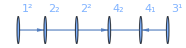

```mathematica
TensorNetworkIndexGraph[tng]
```

### RandomTensorNetwork

RandomTensorNetwork[{n vertex,m edges}, max dimension, max rank]
Given a random graph generated as RandomGraph[{n,m}] for specifying connectivity, then one can specify a max dimension and max rank. Note that vertex degree overwrites the max rank if the max rank is less than vertex degree

maybe instead of max rank, we accept additional rank (as additional tensor legs, so rank would be random[1,vertex degree+additional rank)

```mathematica
tn=RandomTensorNetwork[{4,4},3,2]
```

TensorNetwork[…]

```mathematica
TensorRank/@tn["Tensors"]
```

{3,2,2,2}

```mathematica
TensorDimensions/@tn["Tensors"]
```

{{3,2,3},{2,2},{3,2},{3,2}}

```mathematica
RandomTensorNetwork[{4,4},3,2]["Tensors"]
```

{{{-0.400922-0.675774 ⅈ,-0.341742+0.78452 ⅈ,-0.360016+0.0425217 ⅈ},{0.67753-0.339479 ⅈ,-0.132242+0.463663 ⅈ,-0.449757-0.240483 ⅈ},{-0.17203+0.786093 ⅈ,-0.587471+0.783451 ⅈ,0.653973+0.407294 ⅈ}},{{-0.664671+0.264216 ⅈ,-0.938034+0.559488 ⅈ},{0.580729+0.0064248 ⅈ,-0.77827-0.517972 ⅈ},{0.0448602+0.885219 ⅈ,0.78015+0.916662 ⅈ}},{{-0.423667-0.0760246 ⅈ,-0.993017+0.0921686 ⅈ,-0.394675-0.235423 ⅈ},{0.420644+0.803818 ⅈ,0.13553+0.0284919 ⅈ,0.531536+0.434133 ⅈ}},{{0.409565-0.0255959 ⅈ,0.454707+0.384287 ⅈ},{-0.753628+0.539522 ⅈ,0.256818+0.462552 ⅈ}}}

```mathematica
RandomTensorNetwork[{4,4},3,2,Method->"Complex"]["Tensors"]
```

{{{-0.405747-0.676914 ⅈ,0.605541+0.0701226 ⅈ},{0.0426496-0.173226 ⅈ,0.00569359-0.861742 ⅈ},{-0.0578459+0.927377 ⅈ,0.241014-0.920833 ⅈ}},{{0.551805-0.74025 ⅈ,-0.291582-0.140946 ⅈ},{-0.642521-0.00342866 ⅈ,-0.27367-0.300551 ⅈ}},{-0.994904+0.511605 ⅈ,-0.624169-0.0549352 ⅈ},{{{0.0241722-0.602969 ⅈ,0.351451+0.58013 ⅈ},{-0.931274+0.840849 ⅈ,-0.980997+0.242066 ⅈ},{0.0811505-0.609564 ⅈ,0.415549+0.624212 ⅈ}},{{0.0943159+0.250125 ⅈ,0.96391-0.393568 ⅈ},{-0.585672-0.539861 ⅈ,0.787919+0.195297 ⅈ},{0.0452691+0.191823 ⅈ,0.942185+0.101605 ⅈ}},{{0.921359-0.588493 ⅈ,0.245721+0.487591 ⅈ},{-0.875917-0.845446 ⅈ,-0.966402-0.880978 ⅈ},{-0.421038+0.771297 ⅈ,-0.47985-0.518862 ⅈ}}}}

It take anything as method, if not “Complex” then it treats as real

```mathematica
RandomTensorNetwork[{4,4},3,2,Method->"a"]["Tensors"]
```

{{{-0.275832,-0.246024},{-0.164367,-0.336651}},{{0.419223,-0.517654},{-0.292519,-0.0843638},{-0.00197904,0.0864337}},{{{-0.706033,0.0966249},{0.380955,-0.245803},{-0.687423,0.303477}},{{-0.685588,0.428892},{-0.350707,-0.878134},{-0.00775365,-0.669877}}},{{-0.973258,-0.563536},{-0.382529,-0.550372}}}

### TensorNetworkAdd

Adds a new tensor to an existing network with specified indices.

```mathematica
TensorNetworkGraphData[tng]
```

<|Tensors→{{-0.615629+0.967581 ⅈ,-0.416677+0.171493 ⅈ},{-0.118767+0.183218 ⅈ,-0.977728+0.331289 ⅈ},{{0.233978-0.623686 ⅈ,0.107698-0.28962 ⅈ},{0.459605-0.592967 ⅈ,0.351441+0.556123 ⅈ}},{{-0.641398-0.986184 ⅈ,-0.0643384-0.655265 ⅈ},{0.590714+0.821842 ⅈ,0.789655+0.799814 ⅈ}}},Dimensions→{{2},{2},{2,2},{2,2}},Indices→{{3^1},{1^2},{2^2,2_2},{4_1,4_2}},Vertices→{3,1,2,4},FreeIndices→{},Bonds→{{3^1,4_1}→2,{1^2,2_2}→2,{2^2,4_2}→2},Contractions→{{{3^1,4_1}},{{1^2,2_2}},{{2^2,4_2},{1^2,2_2}},{{3^1,4_1},{2^2,4_2}}},ContractionIndices→{{3^1},{1^2},{2^2,1^2},{3^1,2^2}}|>

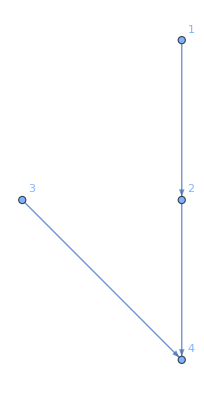
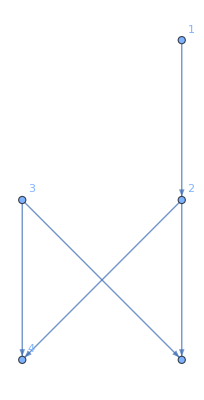
-Graphics-→-Graphics-

```mathematica
tng->TensorNetworkAdd[tng,RandomComplex[{-1-I,1+I},{2,2}],{2^2,3^1}]
```

### TensorNetworkReplaceIndices

### InitializeTensorNetwork

### TensorNetworkToNetGraph

### TensorNetworkRemoveCycles

## Contraction and Path Optimization

```mathematica
tensors={,,,,,,,,,,,,,,};
```

```mathematica
indices={{1,2,22},{12,5,11,19,15},{9,30},{11},{12,13},{14,15,16,17,27},{19,28,29,22},{},{},{},{23,24,25,26},{27,28},{29,30,31},{32,33},{34,35,36,37}};
```

```mathematica
tn=TensorNetwork[tensors,indices](*RandomTensorNetwork[{15,10},3]*)
```

TensorNetwork[…]

```mathematica
finalT=TensorNetworkContract[tn];//Timing
```

{16.1637,Null}

### TensorNetworkFindContractionPath

Finds an optimized contraction path using the Cotengra library.

```mathematica
paths=AssociationMap[TensorNetworkFindContractionPath[tn,Method->#]&,{"Optimal","flops","max","size","write","combo","limit"}]
```

<|Optimal→{{8,10},{8,14},{4,13},{2,12},{3,11},{4,10},{5,9},{3,8},{4,7},{2,6},{1,5},{2,3},{1,3},{1,2}},flops→{{3,13},{7,9},{7,13},{3,12},{2,11},{2,10},{3,5},{2,8},{6,7},{1,6},{4,5},{2,3},{1,3},{1,2}},max→{{3,13},{7,9},{7,13},{3,12},{2,11},{2,10},{2,9},{4,8},{2,7},{5,6},{1,5},{2,3},{1,3},{1,2}},size→{{8,10},{8,14},{4,13},{2,12},{3,11},{4,10},{5,9},{3,8},{4,7},{2,6},{1,5},{2,3},{1,3},{1,2}},write→{{8,10},{8,14},{4,13},{2,12},{3,11},{3,10},{2,6},{2,4},{1,7},{5,6},{4,5},{2,3},{1,3},{1,2}},combo→{{8,10},{8,14},{4,13},{2,12},{3,11},{3,10},{2,6},{2,4},{1,7},{5,6},{4,5},{2,3},{1,3},{1,2}},limit→{{8,10},{8,14},{4,13},{2,12},{3,11},{3,10},{2,6},{2,4},{1,7},{5,6},{4,5},{2,3},{1,3},{1,2}}|>

```mathematica
methods=$TensorNetworkContractionMethods
```

{ArrayDotTranspose,ArrayDot,Dot,TensorContract,TableSum}

```mathematica
tf=Outer[Timing[ActivateTensors[TensorNetworkContraction[tn,#1,Method->#2]]]&,Values[paths],Most[methods],1];
```

```mathematica
tf//Dimensions
```

{7,4,2}

```mathematica
TableForm[tf[[All,All,1]],TableHeadings->{{"Optimal","flops","max","size","write","combo","limit"},Most[methods]}]
```

| ArrayDotTranspose | ArrayDot | Dot | TensorContract
Optimal | 0.066854 | 0.050907 | 0.053481 | 0.050112
flops | 0.05445 | 0.050335 | 0.051341 | 0.04719
max | 0.05154 | 0.048543 | 0.053318 | 0.04932
size | 0.050003 | 0.050597 | 0.055126 | 0.048281
write | 0.048277 | 0.049649 | 0.053269 | 0.05974
combo | 0.048648 | 0.049813 | 0.056412 | 0.063243
limit | 0.051519 | 0.053765 | 0.05402 | 0.057274